Linear Combination of Unitary Operators |

General Implementationpaclet:QuantumMob/Q3/tutorial/LinearCombinationOfUnitaries#221637712 | Example: Success Probabilitypaclet:QuantumMob/Q3/tutorial/LinearCombinationOfUnitaries#1333868550
Examplespaclet:QuantumMob/Q3/tutorial/LinearCombinationOfUnitaries#2113806542 |

Given unitary operators U_1,U_2,…,U_n, let T:=∑_k α_k U_k be a linear combination of those unitary operators, where α_k are complex coefficients. In general, T is not unitary and cannot be implemented directly on a quantum computer. However, using an ancillary qubits, it can be implemented as discussed below.

UniformlyControlledGatepaclet:QuantumMob/Q3/ref/UniformlyControlledGateQuantumMob Package Symbol | Uniformly controlled unitary gates
AmplitudeEncodingpaclet:QuantumMob/Q3/ref/AmplitudeEncodingQuantumMob Package Symbol | Encodes classical data in a quantum state

Q3 functions that are useful to construct a linear combination of unitary operators.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation:

```mathematica
Needs["QuantumMob`Q3`"]
```

General Implementation

Let U_1,U_2,… be unitary operators and α:=(α_1,α_2,…) be a vector of complex numbers.  We want to implement a linear combination T:=∑_k α_k U_k of those unitary operators. Since T is not unitary in general, ancillary qubits are necessary.

One way to implement T is through the quantum circuit shown in Figure 1, where V is a unitary operator with the first column stores the coefficients α_k as follows:

V≐1/(√(‖α‖_1))(√α_1 | * | … | *
√α_2 | * | … | *
⋮ | ⋮ | ⋱ | ⋮
⋮ | * | … | *) .

More specifically, for given coefficients α:=(α_1,α_2,…), the unitary operator V may be implemented by the amplitude encoding gate. The desired operation T is achieved when the ancillary register is measured with all qubits in the 0 state; if not, the procedure fails and must be attempted again. The success probability is given by ψ T^†Tψ/(‖α‖)_1^2. Therefore, the maximum success probability is limited by the squared norm of T; that is, (‖T‖)_2^2/(‖α‖)_1^2.

-Graphics-=-Graphics-

Figure 1. A quantum circuit implementing the linear combination of unitary gates, ∑_k α_k U_k. Here, V^T is a unitary operator the matrix representation of which is given by the transpose of that of V in the computational basis.

When the number of terms is small, the above methods provide a convenient tool to compose a more complicated operation from simpler gates U_k. However, as the number of terms increases, it becomes inefficient in general and the quantum eigenvalue transform (QET) or quantum singular value transform (QSVT) is required.

Examples

```mathematica
Needs["QuantumMob`Q3`"]
```

Refer to the ancillary and system register by symbols A and S:

```mathematica
Let[Qubit,A,S]
```

Consider a system register consisting of n qubits:

```mathematica
$n=1;
SS=S[Range@$n,$]
```

{S_(,,1)}

Take some unitary gates U_k (k=0,…,2^m-1) on the system register:

```mathematica
$m=2;
```

```mathematica
U[k_]:=Rotation[Pi*k/6,S[1,2]]
UU=Table[U[k],{k,Range@Power[2,$m]-1}]
```

{Exp(0),Exp(-1/12 ⅈ π S_(,,1)^(,,Y)),Exp(-1/6 ⅈ π S_(,,1)^(,,Y)),Exp(-1/4 ⅈ π S_(,,1)^(,,Y))}

We will need an ancilla register of m qubits:

```mathematica
AA=A[Range@$m,$]
```

{A_(,,1),A_(,,2)}

### Simple Sum

Consider the sum T:=∑_k U_k of the unitary gates:

```mathematica
TT=Sum[U[k],{k,0,3}]
```

Exp(0)+Exp(-1/12 ⅈ π S_(,,1)^(,,Y))+Exp(-1/6 ⅈ π S_(,,1)^(,,Y))+Exp(-1/4 ⅈ π S_(,,1)^(,,Y))

In general, T is not unitary, and cannot be directly implemented on a quantum computer. However, one can realize it probabilistically with a quantum circuit of the form and post-selection with respect to the ancilla register for state 00…0:

```mathematica
qc=QuantumCircuit[
Ket[AA],
Through[AA[6]],
UniformlyControlledGate[AA,UU,"Label"->"U"],
Through[AA[6]],
"Invisible"->A[$m+1/2]
]
```

-Graphics-

The above quantum circuit is, of course, equivalent to the following one:

```mathematica
Unfold[qc]
```

-Graphics-

To test  it, take an arbitrary input state:

```mathematica
Let[Complex,c]
in=ProductState[S[1]->c@{0,1},"Label"->Ket@{"ψ"}]
```

(c_(,,0) 0+c_(,,1) 1)_(S_(,,1))

```mathematica
full=QuantumCircuit[in,qc]
```

-Graphics-

Take the projection operator onto 00…0:

```mathematica
prj=Dyad[Ket[AA],Ket[AA],AA]
```

0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,1))0_(,,A_(,,2))

```mathematica
out=prj**full
out=KetCanonicalize[KetDrop[out,AA],False]
```

1/16 ((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1)) 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,S_(,,1))+1/16 ((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 0_(,,A_(,,1))0_(,,A_(,,2))1_(,,S_(,,1))

0_(,,S_(,,1))+(((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1))

Compare the above result with the direct operation of T on the input state:

```mathematica
new=Elaborate@KetCanonicalize[TT**in,False]
```

0_(,,S_(,,1))+(((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1))

```mathematica
out-new
```

0

### Linear Superposition

Let us now consider a more general form of linear combination T:=∑_k α_k U_k of the unitary gates:

```mathematica
α={1,1/2,-I,-I/2}
```

{1,1/2,-ⅈ,-ⅈ/2}

```mathematica
TT=α.UU
```

Exp(0)+1/2 (Exp(-1/12 ⅈ π S_(,,1)^(,,Y)))-ⅈ (Exp(-1/6 ⅈ π S_(,,1)^(,,Y)))-1/2 ⅈ (Exp(-1/4 ⅈ π S_(,,1)^(,,Y)))

We fist construct the so-called preparation oracles, V and V^T:

```mathematica
matV=Normal@One[Power[2,$m]];
matV[[1]]=Sqrt[N@α]/Norm[α,1];
matV=Transpose[Chop@Orthogonalize@matV];
matV//MatrixForm
```

(0.57735 | -0.258199 | -0.365148-0.365148 ⅈ | -0.408248-0.408248 ⅈ
0.408248 | 0.912871 | 0 | 0
0.408248-0.408248 ⅈ | -0.182574+0.182574 ⅈ | 0.774597 | 0
0.288675-0.288675 ⅈ | -0.129099+0.129099 ⅈ | -0.365148 | 0.816497)

```mathematica
matV.Topple[matV]//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
VV=Operator[matV,AA,"Label"->"V"]
VT=Operator[Transpose@matV,AA,"Label"->"V^T"]
```

Operator[…]

Operator[…]

Construct the so-called selection oracle, W, which is just given by the uniformly-controlled gate:

```mathematica
WW=UniformlyControlledGate[AA,UU,"Label"->"U"]
```

UniformlyControlledGate[{A_(,,1),A_(,,2)},{Exp(0),Exp(-1/12 ⅈ π S_(,,1)^(,,Y)),Exp(-1/6 ⅈ π S_(,,1)^(,,Y)),Exp(-1/4 ⅈ π S_(,,1)^(,,Y))},Label→U]

Take the overall quantum circuit:

```mathematica
qc=QuantumCircuit[
Ket[AA],in,
VV,WW,VT,
"Invisible"->A@{$m+1/2}
];
Row@{qc,"=",Unfold[qc]}
```

-Graphics-=-Graphics-

Calculate the output state, and perform the post-selection:

```mathematica
out=prj**qc//KetChop;
out=KetCanonicalize[KetDrop[out,AA],False]
```

0_(,,S_(,,1))+(((0.334428-0.300542 ⅈ) c_(,,0)+c_(,,1)) 1_(,,S_(,,1)))/(c_(,,0)-(0.334428-0.300542 ⅈ) c_(,,1))

Compare the result above with the one from directly applying T on the input state:

```mathematica
new=Elaborate@KetCanonicalize[TT**in,False]
```

0_(,,S_(,,1))+(((-4 ⅈ-(1+2 ⅈ) √2+√6) c_(,,0)+(8+(1-2 ⅈ) √2-4 ⅈ √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((8+(1-2 ⅈ) √2-4 ⅈ √3+√6) c_(,,0)+(4 ⅈ+(1+2 ⅈ) √2-√6) c_(,,1))

```mathematica
out-new//Garner//Chop
```

0

Example: Success Probability

Consider the ancillary (labeled as S) and system (labeled as T) registers:

```mathematica
$m=2;
$n=2;
```

```mathematica
Let[Qubit,S,T]
SS=S[Range@$m,$]
TT=T[Range@$n,$]
```

{S_(,,1),S_(,,2)}

{T_(,,1),T_(,,2)}

Consider a set of unitary gates {U_0,U_1,U_2,U_3} on the system register of the form
	U_k:=exp[-ⅈϕ_k(T_1^X T_2^X+T_1^Y T_2^Y+T_1^Z T_2^Z)] .

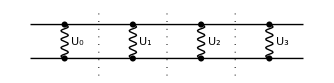

```mathematica
aa={1/6,2/6,4/6,5/6}*Pi;
ex=MapIndexed[
ExchangeExp[#1*{1,1,1},TT,"Label"->Subscript["U",First[#2]-1]]&,
aa
];
QuantumCircuit@@Riffle[ex,"Separator"]
```

We want to operate T:=U_0+U_1+U_2+U_3 on the system register. One can implement it by using the following quantum circuit:

```mathematica
lcu=QuantumCircuit[
S[Range@$m,6],
UniformlyControlledGate[SS,ex],
S[Range@$m,6]
];
Unfold[lcu]
```

-Graphics-

To see how it works, prepare an initial state ψ of the system register:

```mathematica
in=State[{1,1,1,-1}/2,TT,"Label"->Ket@{"ψ"}];
in//Elaborate
```

1/2 0_(,,T_(,,1))0_(,,T_(,,2))+1/2 0_(,,T_(,,1))1_(,,T_(,,2))+1/2 1_(,,T_(,,1))0_(,,T_(,,2))-1/2 1_(,,T_(,,1))1_(,,T_(,,2))

```mathematica
qc=QuantumCircuit[Ket[SS],in,Unfold[lcu]];
full=QuantumCircuit[qc,
"Separator",
Measurement[S[Range@$m,3]],
"PortSize"->{1.25,0.5}
]
```

-Graphics-

Run the above quantum circuit and check the measurement outcomes. If any of the outcomes is non-zero, run the circuit repeatedly until both are zero:

```mathematica
SeedRandom[457];
```

```mathematica
out=Elaborate[full];
KetFactor[out,SS]
```

1_(,,S_(,,1))0_(,,S_(,,2))⊗(1/2 (0_(,,T_(,,1))0_(,,T_(,,2))+0_(,,T_(,,1))1_(,,T_(,,2))+1_(,,T_(,,1))0_(,,T_(,,2))-1_(,,T_(,,1))1_(,,T_(,,2))))

To estimate the success probability, run the circuit many times and collect the statistical data:

```mathematica
mm=Measurements[full]
```

{S_(,,1)^(,,Z),S_(,,2)^(,,Z)}

```mathematica
SeedRandom[457];
```

```mathematica
EchoTiming[
data=Table[Elaborate[full];Readout[mm],100]
];
data=Map[FromDigits[#,2]&,data];
```

3.38469

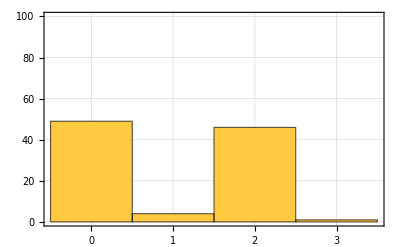

```mathematica
Histogram[data,
PlotRange->{0,100}]
```

To understate the above success probability, calculate the squared norm of operator T, which gives the maximum success probability:

```mathematica
mat=Total[Matrix@ex];
max=Norm[mat,2]^2/16//N//Chop
```

0.466506

For the particular initial state, the success probability is given as follows:

```mathematica
vv=Matrix[in];
prb=Conjugate[vv].ConjugateTranspose[mat].mat.vv/16//N//Chop
```

0.466506

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪A. Gilyen, Y. Su, G. Hao, and N. Wiebe (2019)https://doi.org/10.1145/3313276.3316366, Proceedings of the 51st Annual ACM SIGACT Symposium on Theory of Computing, "Quantum singular value transformation and beyond: exponential improvements for quantum matrix arithmetics."
▪L. Lin (2022)https://arxiv.org/abs/2201.08309, arXiv:2201.08309, "Lecture Notes on Quantum Algorithms for Scientific Computation."
▪J. M. Martyn, Z. M. Rossi, A. K. Tan, I. L. Chuan (2021)https://doi.org/10.1103%2Fprxquantum.2.040203, PRX Quantum 2, 4 040203, "Grand Unification of Quantum Algorithms."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).